# Circule on a sphere

```mathematica
r̂·Subscript[n̂, 1]=Cos[Subscript[α, 1]]
Norm[r̂]=1
```

```mathematica
n1={Cos[ϕ1]Sin[θ1],Sin[ϕ1]Sin[θ1],Cos[θ1]}
r={Cos[ϕ]Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]}
r.n1
```

{Cos[ϕ1] Sin[θ1],Sin[θ1] Sin[ϕ1],Cos[θ1]}

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
Manipulate[ContourPlot[{Cos[θ] Cos[θ1]+Cos[ϕ] Cos[ϕ1] Sin[θ] Sin[θ1]+Sin[θ] Sin[θ1] Sin[ϕ] Sin[ϕ1]==Cos[α1],Cos[θ] Cos[θ2]+Cos[ϕ] Cos[ϕ2] Sin[θ] Sin[θ2]+Sin[θ] Sin[θ2] Sin[ϕ] Sin[ϕ2]==Cos[α2]},{ϕ,0,2Pi},{θ,0,4Pi}, PlotRange->{{0,2 π},{0,π}}, PlotPoints->60, Contours->{0},ContourShading->None,AspectRatio->0.5],{α1,0,π/2,π/10},{θ1,0,π,π/10},{ϕ1,0,2π,π/10},{α2,0,π/2,π/10},{θ2,0,π,π/10},{ϕ2,0,2π,π/10}]
```

## By Spherical symmetric, set the larger circule (blue) on the z - axis. And now found the area

```mathematica
Cos[θ] Cos[θ1]+Cos[ϕ] Cos[ϕ1] Sin[θ] Sin[θ1]+Sin[θ] Sin[θ1] Sin[ϕ] Sin[ϕ1]/.{θ1->0}//Simplify
```

Cos[θ]

```mathematica
Cos[θ] Cos[θ1]+Cos[ϕ] Cos[ϕ1] Sin[θ] Sin[θ1]+Sin[θ] Sin[θ1] Sin[ϕ] Sin[ϕ1]/.{θ1->θ2,ϕ1->π/2}//Simplify
```

Cos[θ] Cos[θ2]+Sin[θ] Sin[θ2] Sin[ϕ]

```mathematica
Cos[θ]==Cos[α1]
Cos[θ] Cos[θ2]+Sin[θ] Sin[θ2] Sin[ϕ]==Cos[α2]
```

```mathematica
Solve[Cos[α1] Cos[θ2]+Sin[α1] Sin[θ2] Sin[ϕ]==Cos[α2],ϕ]//Simplify
```

{{ϕ→-ArcSin[Cot[α1] Cot[θ2]-Cos[α2] Csc[α1] Csc[θ2]]}}

```mathematica
H=θ/.Solve[Cos[θ] Cos[θ2]+Sin[θ] Sin[θ2] Sin[ϕ]==Cos[α2],θ]//Simplify
```

{-ArcCos[(Cos[α2] Cos[θ2]-Sin[ϕ] √(Cos[θ2]^2 (-Cos[α2]^2+Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)) Tan[θ2])/(Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)],ArcCos[(Cos[α2] Cos[θ2]-Sin[ϕ] √(Cos[θ2]^2 (-Cos[α2]^2+Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)) Tan[θ2])/(Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)],-ArcCos[(Cos[α2] Cos[θ2]+Sin[ϕ] √(Cos[θ2]^2 (-Cos[α2]^2+Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)) Tan[θ2])/(Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)],ArcCos[(Cos[α2] Cos[θ2]+Sin[ϕ] √(Cos[θ2]^2 (-Cos[α2]^2+Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)) Tan[θ2])/(Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)]}

```mathematica
Manipulate[Plot[{α1,ArcCos[(Cos[α2] Cos[θ2]-Sin[ϕ] √(Cos[θ2]^2 (-Cos[α2]^2+Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)) Tan[θ2])/(Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)],ArcCos[(Cos[α2] Cos[θ2]+Sin[ϕ] √(Cos[θ2]^2 (-Cos[α2]^2+Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)) Tan[θ2])/(Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)]},{ϕ,0, 2π}, PlotRange->{{0,2π},{0,π}}],{α1,0,π/2},{α2,0,π/2},{θ2,0,π}]
```

```mathematica
ArcCos[(Cos[α2] Cos[θ2]+Sin[ϕ] √(Cos[θ2]^2 (-Cos[α2]^2+Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)) Tan[θ2])/(Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)]/.{ϕ->α1}
```

ArcCos[(Cos[α2] Cos[θ2]+Sin[α1] √(Cos[θ2]^2 (-Cos[α2]^2+Cos[θ2]^2+Sin[α1]^2 Sin[θ2]^2)) Tan[θ2])/(Cos[θ2]^2+Sin[α1]^2 Sin[θ2]^2)]

### Area

```mathematica
Integrate[Integrate[ Sin[θ],{θ,ArcCos[(Cos[α2] Cos[θ2]+Sin[ϕ] √(Cos[θ2]^2 (-Cos[α2]^2+Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)) Tan[θ2])/(Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)], α1}],{ϕ,A, B}]
```

```mathematica
Integrate[Cos[(Cos[α2] Cos[θ2]+Sin[ϕ] √(Cos[θ2]^2 (-Cos[α2]^2+Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)) Tan[θ2])/(Cos[θ2]^2+Sin[θ2]^2 Sin[ϕ]^2)]-Cos[α1],{ϕ,A,B}]
```

$Aborted

## Circule on Sphere Plot

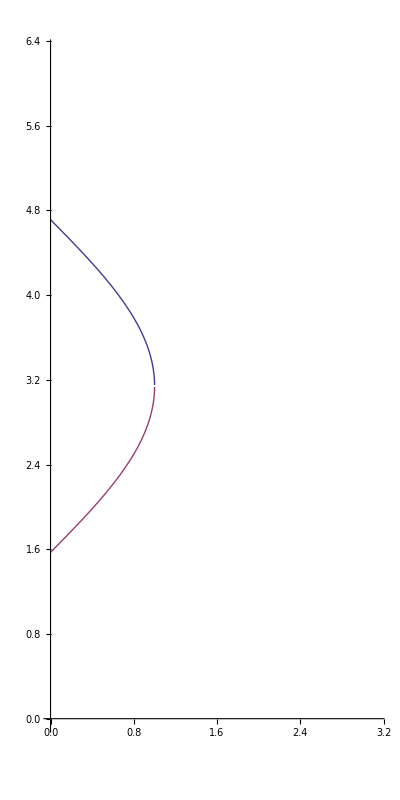

```mathematica
f1[θ_]:=ArcCos[θ]+π;
f2[θ_]:=ArcCos[-θ];
np=50;
Plot[{f1[θ],f2[θ]},{θ,0,π},PlotRange->{{0,π},{0,2π}},AspectRatio->2]
```

```mathematica
Show[
SphericalPlot3D[1,{θ,0,Pi},{ϕ,0,2Pi},Mesh->None,PlotStyle->Opacity[0.4]],
ParametricPlot3D[
{{Cos[f1[θ]]Sin[θ],Sin[f1[θ]]Sin[θ],Cos[θ]},
{Cos[f2[θ]]Sin[θ],Sin[f2[θ]]Sin[θ],Cos[θ]}},
{θ,0,π}]
]
```

-Graphics3D-

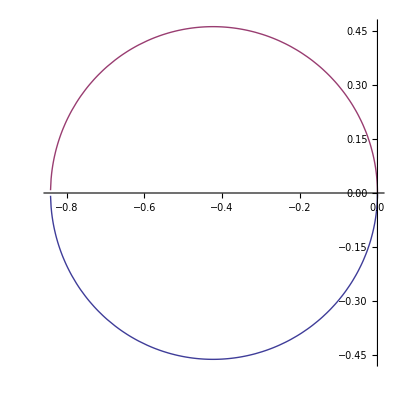

```mathematica
ParametricPlot[
{{Cos[f1[θ]]Sin[θ],Sin[f1[θ]]Sin[θ]},
{Cos[f2[θ]]Sin[θ],Sin[f2[θ]]Sin[θ]}},
{θ,0,π},AspectRatio->1]
```

```mathematica
Manipulate[
ContourPlot[
{Cos[ϕ-ϕ1] Sin[θ]==Cos[α1],
Cos[ϕ]Sin[θ]==Cos[α2]}
,{θ,0,4Pi},{ϕ,0,2Pi}, PlotRange->{{0, π},{0,2π}}, PlotPoints->60, Contours->{0},ContourShading->None,AspectRatio->2],{α1,0,π/2},{α2,0,π/2},{ϕ1,0,π}]
```

```mathematica
Manipulate[
ContourPlot[
{Cos[ϕ-ϕ1] Sin[θ]==Cos[α1],
Cos[ϕ]Sin[θ]==Cos[α2]}
,{ϕ,0,2Pi},{θ,0,4Pi}, PlotRange->{{0, 2π},{0,π}}, PlotPoints->60, Contours->{0},ContourShading->None,AspectRatio->0.5],{α1,0,π/2},{α2,0,π/2},{ϕ1,0,π}]
```

```mathematica
Solve[Cos[ϕ-ϕ1]==Cos[α1]/Cos[α2] Cos[ϕ],ϕ]//Simplify
```

{{ϕ→-ArcCos[(√((Cos[ϕ1]-Cos[α1] Sec[α2])^2) Sin[ϕ1])/((-Cos[ϕ1]+Cos[α1] Sec[α2]) √(Cos[ϕ1]^2-2 Cos[α1] Cos[ϕ1] Sec[α2]+Cos[α1]^2 Sec[α2]^2+Sin[ϕ1]^2))]},{ϕ→ArcCos[(√((Cos[ϕ1]-Cos[α1] Sec[α2])^2) Sin[ϕ1])/((-Cos[ϕ1]+Cos[α1] Sec[α2]) √(Cos[ϕ1]^2-2 Cos[α1] Cos[ϕ1] Sec[α2]+Cos[α1]^2 Sec[α2]^2+Sin[ϕ1]^2))]},{ϕ→-ArcCos[(√((Cos[ϕ1]-Cos[α1] Sec[α2])^2) Sin[ϕ1])/((Cos[ϕ1]-Cos[α1] Sec[α2]) √(Cos[ϕ1]^2-2 Cos[α1] Cos[ϕ1] Sec[α2]+Cos[α1]^2 Sec[α2]^2+Sin[ϕ1]^2))]},{ϕ→ArcCos[(√((Cos[ϕ1]-Cos[α1] Sec[α2])^2) Sin[ϕ1])/((Cos[ϕ1]-Cos[α1] Sec[α2]) √(Cos[ϕ1]^2-2 Cos[α1] Cos[ϕ1] Sec[α2]+Cos[α1]^2 Sec[α2]^2+Sin[ϕ1]^2))]}}